## Definiciones

## Operadores

### Coin

```mathematica
-Graphics-;
```

```mathematica
n[α_,ϕ_]:={Sin[α]Cos[ϕ],Sin[α]Sin[ϕ],Cos[α]}
```

```mathematica
Paulis=PauliMatrix/@Range[3];
```

```mathematica
expCoin[θ_,α_,ϕ_]:=MatrixExp[(-ⅈ θ)/2(n[α,ϕ].Paulis)]
```

```mathematica
Coin[θ_,α_,ϕ_,t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1,{i,2 t+1}]],SparseArray[expCoin[θ,α,ϕ]]]
```

```mathematica
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
Coin[θ,α,ϕ,t]
```

SparseArray[…]

### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*(2*t+1)]
```

```mathematica
t=1;
Shift[t].{0,0,1,0,0,0}
```

{0,0,0,0,1,0}

### Unitaria

```mathematica
Unitary[θ_,α_,ϕ_,t_Integer]:=Shift[t].Coin[θ,α,ϕ,t]
```

```mathematica
θ=0.52π;
α=0.23π;
ϕ=1.75π;
Unitary[θ,α,ϕ,2].ArrayPad[Unitary[θ,α,ϕ,1].{0,0,1,0,0,0},2]//FullSimplify//Chop
```

{0,-0.0469526-0.419743 ⅈ,0,0,-0.232397,-0.419743-0.0469526 ⅈ,0,0,0.169606-0.748631 ⅈ,0}

```mathematica
Unitary[paramsCoin_List,t_Integer]:=Module[{coinProduct},
coinProduct=Dot@@(Coin[##,t]&@@@Reverse[paramsCoin]);
Shift[t].coinProduct]
```

```mathematica
θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;

Unitary[params,t]//Normal
Shift[t].Dot@@(Coin[##,t]&@@@Reverse[{{θ1,α1,ϕ1},{θ2,α2,ϕ2}}])//Normal
Shift[t].Coin[θ2,α2,ϕ2,t].Coin[θ1,α1,ϕ1,t]//Normal
```

{{0,0,0,0,0,0},{0,0,1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),1/8 (-1)^(1/10) (-5+√5)+1/8 (-1)^(9/10) (3+√5),0,0},{1/8 (-1)^(1/10) (-3-√5)+1/8 (-1)^(9/10) (5-√5),1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),0,0,0,0},{0,0,0,0,1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),1/8 (-1)^(1/10) (-5+√5)+1/8 (-1)^(9/10) (3+√5)},{0,0,1/8 (-1)^(1/10) (-3-√5)+1/8 (-1)^(9/10) (5-√5),1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),0,0},{0,0,0,0,0,0}}

{{0,0,0,0,0,0},{0,0,1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),1/8 (-1)^(1/10) (-5+√5)+1/8 (-1)^(9/10) (3+√5),0,0},{1/8 (-1)^(1/10) (-3-√5)+1/8 (-1)^(9/10) (5-√5),1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),0,0,0,0},{0,0,0,0,1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),1/8 (-1)^(1/10) (-5+√5)+1/8 (-1)^(9/10) (3+√5)},{0,0,1/8 (-1)^(1/10) (-3-√5)+1/8 (-1)^(9/10) (5-√5),1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),0,0},{0,0,0,0,0,0}}

{{0,0,0,0,0,0},{0,0,1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),1/8 (-1)^(1/10) (-5+√5)+1/8 (-1)^(9/10) (3+√5),0,0},{1/8 (-1)^(1/10) (-3-√5)+1/8 (-1)^(9/10) (5-√5),1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),0,0,0,0},{0,0,0,0,1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),1/8 (-1)^(1/10) (-5+√5)+1/8 (-1)^(9/10) (3+√5)},{0,0,1/8 (-1)^(1/10) (-3-√5)+1/8 (-1)^(9/10) (5-√5),1/4 (-1)^(1/10) √(1/2 (5+√5))+1/4 (-1)^(9/10) √(1/2 (5+√5)),0,0},{0,0,0,0,0,0}}

## Funciones cálculos

### Estados de la moneda

```mathematica
state0={1.,0.};
state1={0.,1.};
plusX=1/Sqrt[2]{1.,1.};
minusX=1/Sqrt[2]{1.,-1.};
plusY=1/Sqrt[2.]{1,ⅈ};
minusY=1/Sqrt[2.]{1,-ⅈ};
```

```mathematica
HVecs=N[Normalize/@Eigenvectors[FourierMatrix[2]]];
HMinus=HVecs[[1]];
HPlus=HVecs[[2]];
```

### Hallar antípoda

```mathematica
FindAntipode[polar_,azimutal_]:=Module[{newPolar,newAzimutal},
{newPolar=π-polar,
newAzimutal=azimutal+π}
]
```

```mathematica
α=6π/10;
ϕ=0;
FindAntipode[α,ϕ]
```

{(2 π)/5,π}

### Estado final de la caminata después de t pasos

```mathematica
DQWL[coin0_,θ_,α_,ϕ_,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[θ,α,ϕ,i]],{i,t}];
psi
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
DQWL[coin0,θ,α,ϕ,t]
```

{0,-0.672499+0.275336 ⅈ,0,0,-0.672499+0.140291 ⅈ,0}

```mathematica
DQWL[coin0_,paramsCoin_List,t_Integer]:=
Module[{psi},
psi=coin0;
Do[psi=Chop[#.ArrayPad[psi,2]]&[Unitary[paramsCoin,i]],{i,t}];
psi
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};

θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;
DQWL[coin0,params,t]
```

{0,-0.672499+0.275336 ⅈ,0,0,-0.672499+0.140291 ⅈ,0}

### Distribución de probabilidad

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2(2tmax+1),2]]
```

```mathematica
coin0=state0;
θ=0.52π;
α=0.23π;
ϕ=1.75π;
t=3;
PosProbDistrib[DQWL[coin0,θ,α,ϕ,t],t]
```

{0.136932,0,0.108026,0,0.302759,0,0.452283}

### Distribución de probabilidad para cada uno de los pasos

```mathematica
PosProbDisTime[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@θ,N@α,N@ϕ,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;
P1=PosProbDisTime[coin0,θ,α,ϕ,t]
```

{{0,1.,0},{0.528064,0,0.471936}}

```mathematica
PosProbDisTime[coin0_,paramsCoin_List,t_Integer]:=Module[{psi,probs,p},
psi=coin0;
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=Chop[#.ArrayPad[psi,2]]&[Unitary[N@paramsCoin,i]];
ArrayPad[probs,t-(i-1)],{i,t+1}];
p
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};

θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;
P2=PosProbDisTime[coin0,params,t]
```

{{0,1.,0},{0.528064,0,0.471936}}

### Valor de expectación

```mathematica
ExpecValue[posProbDisTime_List, t_Integer]:=Flatten[Chop[posProbDisTime.Range[-t,t]]]
```

```mathematica
t=1;
EV=ExpecValue[P2, t]
```

{0,-0.0561285}

### Determinar si la estrategia es ganadora o perdedora

```mathematica
WinningQ[expValsList_List] := 
  Which[
SameQ@@expValsList,"Indefinido",
    OrderedQ[expValsList], "Ganadora",
    OrderedQ[expValsList, GreaterEqual], "Perdedora",
    True, "No se puede determinar"
  ]
```

```mathematica
WinningQ[EV]
```

Perdedora

### Calcular posProbDistTime, expval y typeStrategy

```mathematica
CalculateData[coin0_,θ_,α_,ϕ_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,θ,α,ϕ,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};
θ=9π/5;
α=2 π/5;
ϕ=π;
t=1;

CalculateData[coin0,θ,α,ϕ,t]
```

{{{0,1.,0},{0.528064,0,0.471936}},{0,-0.0561285},Perdedora}

```mathematica
CalculateData[coin0_,paramsCoin_,t_Integer]:=Module[{posProbDistTime,expval,typeStrategy},
{posProbDistTime=PosProbDisTime[coin0,paramsCoin,t],
expval=ExpecValue[posProbDistTime,t],
typeStrategy=WinningQ[expval]}
]
```

```mathematica
coin0=1/Sqrt[2]{1.,1.};

θ1=9π/5;
α1=2 π/5;
ϕ1=π;

θ2=0;
α2=0;
ϕ2=2π;

params={{θ1,α1,ϕ1},{θ2,α2,ϕ2}};

t=1;
CalculateData[coin0,params,t]
```

{{{0,1.,0},{0.528064,0,0.471936}},{0,-0.0561285},Perdedora}

### Fijar θ y α, variar ϕ

```mathematica
VaryingPhi[coin0_,θ_,α_,nϕ_Integer,t_Integer]:=Module[{ϕ},
Table[
Flatten[{ϕ=i *2π/nϕ,
CalculateData[coin0,θ,α,ϕ,t]},
1],
{i,0,nϕ-1}
]
]
```

```mathematica
coin0=plusX;
θ=9π/5;
α=2 π/5;
nϕ=2;
t=1;
A=VaryingPhi[coin0,θ,α,nϕ,t]
```

{{0,{{0,1.,0},{0.471936,0,0.528064}},{0,0.0561285},Ganadora},{π,{{0,1.,0},{0.528064,0,0.471936}},{0,-0.0561285},Perdedora}}

### Fijar θ , variar α y ϕ

```mathematica
VaryingAlpha[coin0_,θ_,nα_Integer,nϕ_Integer,t_Integer]:=Module[{α},
Flatten[
Table[α=j*Pi/(nα-1);
Map[Prepend[#,α]&,
VaryingPhi[coin0,θ,α,nϕ,t]
],
{j,0,nα-1}],
1]
]
```

```mathematica
coin0=plusX;
θ=9π/5;
nα=2;
nϕ=2;
t=1;
B=VaryingAlpha[coin0,θ,nα,nϕ,t]
```

{{0,0,{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido},{0,π,{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido},{π,0,{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido},{π,π,{{0,1.,0},{0.5,0,0.5}},{0,0},Indefinido}}

### Variar θ, α y ϕ

```mathematica
VaryingTheta[psi0_,nθ_Integer,nα_Integer,nϕ_Integer,t_Integer]:=Module[{θ},
Flatten[Table[θ=k*2*Pi/nθ;
Map[Prepend[#,θ]&,
VaryingAlpha[psi0,θ,nα,nϕ,t]
],
{k,0,nθ-1}],
1]
]
```

```mathematica
coin0=minusX;
nθ=10;
nα=10;
nϕ=10;
t=10;
F=VaryingTheta[coin0,nθ,nα,nϕ,t];
#[[5,-1]]&/@F
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.492013,0.549135,1.38053,1.68461,1.34523,0.492013,-0.549135,-1.38053,-1.68461,-1.34523,-0.504674,0.783499,1.7724,2.08431,1.60008,0.504674,-0.783499,-1.7724,-2.08431,-1.60008,-0.375491,1.05476,2.08213,2.31419,1.66232,0.375491,-1.05476,-2.08213,-2.31419,-1.66232,-0.146169,1.40449,2.41868,2.50902,1.64099,0.146169,-1.40449,-2.41868,-2.50902,-1.64099,0.146169,1.64099,2.50902,2.41868,1.40449,-0.146169,-1.64099,-2.50902,-2.41868,-1.40449,0.375491,1.66232,2.31419,2.08213,1.05476,-0.375491,-1.66232,-2.31419,-2.08213,-1.05476,0.504674,1.60008,2.08431,1.7724,0.783499,-0.504674,-1.60008,-2.08431,-1.7724,-0.783499,0.492013,1.34523,1.68461,1.38053,0.549135,-0.492013,-1.34523,-1.68461,-1.38053,-0.549135,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.18102,0.0613198,1.28024,2.01015,1.97226,1.18102,-0.0613198,-1.28024,-2.01015,-1.97226,-1.5213,0.375883,2.12949,3.06971,2.8374,1.5213,-0.375883,-2.12949,-3.06971,-2.8374,-1.10066,0.890454,2.54145,3.22169,2.67136,1.10066,-0.890454,-2.54145,-3.22169,-2.67136,-0.418103,1.60967,3.0226,3.281,2.28617,0.418103,-1.60967,-3.0226,-3.281,-2.28617,0.418103,2.28617,3.281,3.0226,1.60967,-0.418103,-2.28617,-3.281,-3.0226,-1.60967,1.10066,2.67136,3.22169,2.54145,0.890454,-1.10066,-2.67136,-3.22169,-2.54145,-0.890454,1.5213,2.8374,3.06971,2.12949,0.375883,-1.5213,-2.8374,-3.06971,-2.12949,-0.375883,1.18102,1.97226,2.01015,1.28024,0.0613198,-1.18102,-1.97226,-2.01015,-1.28024,-0.0613198,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.89655,-0.672439,0.808523,1.98066,2.39625,1.89655,0.672439,-0.808523,-1.98066,-2.39625,-2.33795,-0.588093,1.3864,2.83134,3.1948,2.33795,0.588093,-1.3864,-2.83134,-3.1948,-1.88629,0.0850431,2.02389,3.18968,3.13712,1.88629,-0.0850431,-2.02389,-3.18968,-3.13712,-0.683467,1.12791,2.50846,2.93087,2.23378,0.683467,-1.12791,-2.50846,-2.93087,-2.23378,0.683467,2.23378,2.93087,2.50846,1.12791,-0.683467,-2.23378,-2.93087,-2.50846,-1.12791,1.88629,3.13712,3.18968,2.02389,0.0850431,-1.88629,-3.13712,-3.18968,-2.02389,-0.0850431,2.33795,3.1948,2.83134,1.3864,-0.588093,-2.33795,-3.1948,-2.83134,-1.3864,0.588093,1.89655,2.39625,1.98066,0.808523,-0.672439,-1.89655,-2.39625,-1.98066,-0.808523,0.672439,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.60875,-1.58032,0.0517368,1.66403,2.64072,2.60875,1.58032,-0.0517368,-1.66403,-2.64072,-3.17555,-1.77737,0.299696,2.26229,3.36077,3.17555,1.77737,-0.299696,-2.26229,-3.36077,-2.45215,-1.04719,0.757755,2.27327,2.92047,2.45215,1.04719,-0.757755,-2.27327,-2.92047,-0.844702,0.245648,1.24217,1.76422,1.6124,0.844702,-0.245648,-1.24217,-1.76422,-1.6124,0.844702,1.6124,1.76422,1.24217,0.245648,-0.844702,-1.6124,-1.76422,-1.24217,-0.245648,2.45215,2.92047,2.27327,0.757755,-1.04719,-2.45215,-2.92047,-2.27327,-0.757755,1.04719,3.17555,3.36077,2.26229,0.299696,-1.77737,-3.17555,-3.36077,-2.26229,-0.299696,1.77737,2.60875,2.64072,1.66403,0.0517368,-1.58032,-2.60875,-2.64072,-1.66403,-0.0517368,1.58032,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.89115,-2.33899,-0.893415,0.893415,2.33899,2.89115,2.33899,0.893415,-0.893415,-2.33899,-3.50332,-2.83425,-1.08259,1.08259,2.83425,3.50332,2.83425,1.08259,-1.08259,-2.83425,-2.67317,-2.16264,-0.826056,0.826056,2.16264,2.67317,2.16264,0.826056,-0.826056,-2.16264,-0.913419,-0.738972,-0.282262,0.282262,0.738972,0.913419,0.738972,0.282262,-0.282262,-0.738972,0.913419,0.738972,0.282262,-0.282262,-0.738972,-0.913419,-0.738972,-0.282262,0.282262,0.738972,2.67317,2.16264,0.826056,-0.826056,-2.16264,-2.67317,-2.16264,-0.826056,0.826056,2.16264,3.50332,2.83425,1.08259,-1.08259,-2.83425,-3.50332,-2.83425,-1.08259,1.08259,2.83425,2.89115,2.33899,0.893415,-0.893415,-2.33899,-2.89115,-2.33899,-0.893415,0.893415,2.33899,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.60875,-2.64072,-1.66403,-0.0517368,1.58032,2.60875,2.64072,1.66403,0.0517368,-1.58032,-3.17555,-3.36077,-2.26229,-0.299696,1.77737,3.17555,3.36077,2.26229,0.299696,-1.77737,-2.45215,-2.92047,-2.27327,-0.757755,1.04719,2.45215,2.92047,2.27327,0.757755,-1.04719,-0.844702,-1.6124,-1.76422,-1.24217,-0.245648,0.844702,1.6124,1.76422,1.24217,0.245648,0.844702,-0.245648,-1.24217,-1.76422,-1.6124,-0.844702,0.245648,1.24217,1.76422,1.6124,2.45215,1.04719,-0.757755,-2.27327,-2.92047,-2.45215,-1.04719,0.757755,2.27327,2.92047,3.17555,1.77737,-0.299696,-2.26229,-3.36077,-3.17555,-1.77737,0.299696,2.26229,3.36077,2.60875,1.58032,-0.0517368,-1.66403,-2.64072,-2.60875,-1.58032,0.0517368,1.66403,2.64072,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.89655,-2.39625,-1.98066,-0.808523,0.672439,1.89655,2.39625,1.98066,0.808523,-0.672439,-2.33795,-3.1948,-2.83134,-1.3864,0.588093,2.33795,3.1948,2.83134,1.3864,-0.588093,-1.88629,-3.13712,-3.18968,-2.02389,-0.0850431,1.88629,3.13712,3.18968,2.02389,0.0850431,-0.683467,-2.23378,-2.93087,-2.50846,-1.12791,0.683467,2.23378,2.93087,2.50846,1.12791,0.683467,-1.12791,-2.50846,-2.93087,-2.23378,-0.683467,1.12791,2.50846,2.93087,2.23378,1.88629,-0.0850431,-2.02389,-3.18968,-3.13712,-1.88629,0.0850431,2.02389,3.18968,3.13712,2.33795,0.588093,-1.3864,-2.83134,-3.1948,-2.33795,-0.588093,1.3864,2.83134,3.1948,1.89655,0.672439,-0.808523,-1.98066,-2.39625,-1.89655,-0.672439,0.808523,1.98066,2.39625,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.18102,-1.97226,-2.01015,-1.28024,-0.0613198,1.18102,1.97226,2.01015,1.28024,0.0613198,-1.5213,-2.8374,-3.06971,-2.12949,-0.375883,1.5213,2.8374,3.06971,2.12949,0.375883,-1.10066,-2.67136,-3.22169,-2.54145,-0.890454,1.10066,2.67136,3.22169,2.54145,0.890454,-0.418103,-2.28617,-3.281,-3.0226,-1.60967,0.418103,2.28617,3.281,3.0226,1.60967,0.418103,-1.60967,-3.0226,-3.281,-2.28617,-0.418103,1.60967,3.0226,3.281,2.28617,1.10066,-0.890454,-2.54145,-3.22169,-2.67136,-1.10066,0.890454,2.54145,3.22169,2.67136,1.5213,-0.375883,-2.12949,-3.06971,-2.8374,-1.5213,0.375883,2.12949,3.06971,2.8374,1.18102,-0.0613198,-1.28024,-2.01015,-1.97226,-1.18102,0.0613198,1.28024,2.01015,1.97226,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.492013,-1.34523,-1.68461,-1.38053,-0.549135,0.492013,1.34523,1.68461,1.38053,0.549135,-0.504674,-1.60008,-2.08431,-1.7724,-0.783499,0.504674,1.60008,2.08431,1.7724,0.783499,-0.375491,-1.66232,-2.31419,-2.08213,-1.05476,0.375491,1.66232,2.31419,2.08213,1.05476,-0.146169,-1.64099,-2.50902,-2.41868,-1.40449,0.146169,1.64099,2.50902,2.41868,1.40449,0.146169,-1.40449,-2.41868,-2.50902,-1.64099,-0.146169,1.40449,2.41868,2.50902,1.64099,0.375491,-1.05476,-2.08213,-2.31419,-1.66232,-0.375491,1.05476,2.08213,2.31419,1.66232,0.504674,-0.783499,-1.7724,-2.08431,-1.60008,-0.504674,0.783499,1.7724,2.08431,1.60008,0.492013,-0.549135,-1.38053,-1.68461,-1.34523,-0.492013,0.549135,1.38053,1.68461,1.34523,0,0,0,0,0,0,0,0,0,0}

```mathematica
Module[{th},
th=F[[1]];
Flatten[{#[[2;;3]],#[[5,-1]]}]&/@F
]
```

{{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,0},{π/9,π/5,0},{π/9,(2 π)/5,0},{π/9,(3 π)/5,0},{π/9,(4 π)/5,0},{π/9,π,0},{π/9,(6 π)/5,0},{π/9,(7 π)/5,0},{π/9,(8 π)/5,0},{π/9,(9 π)/5,0},{(2 π)/9,0,0},{(2 π)/9,π/5,0},{(2 π)/9,(2 π)/5,0},{(2 π)/9,(3 π)/5,0},{(2 π)/9,(4 π)/5,0},{(2 π)/9,π,0},{(2 π)/9,(6 π)/5,0},{(2 π)/9,(7 π)/5,0},{(2 π)/9,(8 π)/5,0},{(2 π)/9,(9 π)/5,0},{π/3,0,0},{π/3,π/5,0},{π/3,(2 π)/5,0},{π/3,(3 π)/5,0},{π/3,(4 π)/5,0},{π/3,π,0},{π/3,(6 π)/5,0},{π/3,(7 π)/5,0},{π/3,(8 π)/5,0},{π/3,(9 π)/5,0},{(4 π)/9,0,0},{(4 π)/9,π/5,0},{(4 π)/9,(2 π)/5,0},{(4 π)/9,(3 π)/5,0},{(4 π)/9,(4 π)/5,0},{(4 π)/9,π,0},{(4 π)/9,(6 π)/5,0},{(4 π)/9,(7 π)/5,0},{(4 π)/9,(8 π)/5,0},{(4 π)/9,(9 π)/5,0},{(5 π)/9,0,0},{(5 π)/9,π/5,0},{(5 π)/9,(2 π)/5,0},{(5 π)/9,(3 π)/5,0},{(5 π)/9,(4 π)/5,0},{(5 π)/9,π,0},{(5 π)/9,(6 π)/5,0},{(5 π)/9,(7 π)/5,0},{(5 π)/9,(8 π)/5,0},{(5 π)/9,(9 π)/5,0},{(2 π)/3,0,0},{(2 π)/3,π/5,0},{(2 π)/3,(2 π)/5,0},{(2 π)/3,(3 π)/5,0},{(2 π)/3,(4 π)/5,0},{(2 π)/3,π,0},{(2 π)/3,(6 π)/5,0},{(2 π)/3,(7 π)/5,0},{(2 π)/3,(8 π)/5,0},{(2 π)/3,(9 π)/5,0},{(7 π)/9,0,0},{(7 π)/9,π/5,0},{(7 π)/9,(2 π)/5,0},{(7 π)/9,(3 π)/5,0},{(7 π)/9,(4 π)/5,0},{(7 π)/9,π,0},{(7 π)/9,(6 π)/5,0},{(7 π)/9,(7 π)/5,0},{(7 π)/9,(8 π)/5,0},{(7 π)/9,(9 π)/5,0},{(8 π)/9,0,0},{(8 π)/9,π/5,0},{(8 π)/9,(2 π)/5,0},{(8 π)/9,(3 π)/5,0},{(8 π)/9,(4 π)/5,0},{(8 π)/9,π,0},{(8 π)/9,(6 π)/5,0},{(8 π)/9,(7 π)/5,0},{(8 π)/9,(8 π)/5,0},{(8 π)/9,(9 π)/5,0},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0},{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,-0.492013},{π/9,π/5,0.549135},{π/9,(2 π)/5,1.38053},{π/9,(3 π)/5,1.68461},{π/9,(4 π)/5,1.34523},{π/9,π,0.492013},{π/9,(6 π)/5,-0.549135},{π/9,(7 π)/5,-1.38053},{π/9,(8 π)/5,-1.68461},{π/9,(9 π)/5,-1.34523},{(2 π)/9,0,-0.504674},{(2 π)/9,π/5,0.783499},{(2 π)/9,(2 π)/5,1.7724},{(2 π)/9,(3 π)/5,2.08431},{(2 π)/9,(4 π)/5,1.60008},{(2 π)/9,π,0.504674},{(2 π)/9,(6 π)/5,-0.783499},{(2 π)/9,(7 π)/5,-1.7724},{(2 π)/9,(8 π)/5,-2.08431},{(2 π)/9,(9 π)/5,-1.60008},{π/3,0,-0.375491},{π/3,π/5,1.05476},{π/3,(2 π)/5,2.08213},{π/3,(3 π)/5,2.31419},{π/3,(4 π)/5,1.66232},{π/3,π,0.375491},{π/3,(6 π)/5,-1.05476},{π/3,(7 π)/5,-2.08213},{π/3,(8 π)/5,-2.31419},{π/3,(9 π)/5,-1.66232},{(4 π)/9,0,-0.146169},{(4 π)/9,π/5,1.40449},{(4 π)/9,(2 π)/5,2.41868},{(4 π)/9,(3 π)/5,2.50902},{(4 π)/9,(4 π)/5,1.64099},{(4 π)/9,π,0.146169},{(4 π)/9,(6 π)/5,-1.40449},{(4 π)/9,(7 π)/5,-2.41868},{(4 π)/9,(8 π)/5,-2.50902},{(4 π)/9,(9 π)/5,-1.64099},{(5 π)/9,0,0.146169},{(5 π)/9,π/5,1.64099},{(5 π)/9,(2 π)/5,2.50902},{(5 π)/9,(3 π)/5,2.41868},{(5 π)/9,(4 π)/5,1.40449},{(5 π)/9,π,-0.146169},{(5 π)/9,(6 π)/5,-1.64099},{(5 π)/9,(7 π)/5,-2.50902},{(5 π)/9,(8 π)/5,-2.41868},{(5 π)/9,(9 π)/5,-1.40449},{(2 π)/3,0,0.375491},{(2 π)/3,π/5,1.66232},{(2 π)/3,(2 π)/5,2.31419},{(2 π)/3,(3 π)/5,2.08213},{(2 π)/3,(4 π)/5,1.05476},{(2 π)/3,π,-0.375491},{(2 π)/3,(6 π)/5,-1.66232},{(2 π)/3,(7 π)/5,-2.31419},{(2 π)/3,(8 π)/5,-2.08213},{(2 π)/3,(9 π)/5,-1.05476},{(7 π)/9,0,0.504674},{(7 π)/9,π/5,1.60008},{(7 π)/9,(2 π)/5,2.08431},{(7 π)/9,(3 π)/5,1.7724},{(7 π)/9,(4 π)/5,0.783499},{(7 π)/9,π,-0.504674},{(7 π)/9,(6 π)/5,-1.60008},{(7 π)/9,(7 π)/5,-2.08431},{(7 π)/9,(8 π)/5,-1.7724},{(7 π)/9,(9 π)/5,-0.783499},{(8 π)/9,0,0.492013},{(8 π)/9,π/5,1.34523},{(8 π)/9,(2 π)/5,1.68461},{(8 π)/9,(3 π)/5,1.38053},{(8 π)/9,(4 π)/5,0.549135},{(8 π)/9,π,-0.492013},{(8 π)/9,(6 π)/5,-1.34523},{(8 π)/9,(7 π)/5,-1.68461},{(8 π)/9,(8 π)/5,-1.38053},{(8 π)/9,(9 π)/5,-0.549135},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0},{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,-1.18102},{π/9,π/5,0.0613198},{π/9,(2 π)/5,1.28024},{π/9,(3 π)/5,2.01015},{π/9,(4 π)/5,1.97226},{π/9,π,1.18102},{π/9,(6 π)/5,-0.0613198},{π/9,(7 π)/5,-1.28024},{π/9,(8 π)/5,-2.01015},{π/9,(9 π)/5,-1.97226},{(2 π)/9,0,-1.5213},{(2 π)/9,π/5,0.375883},{(2 π)/9,(2 π)/5,2.12949},{(2 π)/9,(3 π)/5,3.06971},{(2 π)/9,(4 π)/5,2.8374},{(2 π)/9,π,1.5213},{(2 π)/9,(6 π)/5,-0.375883},{(2 π)/9,(7 π)/5,-2.12949},{(2 π)/9,(8 π)/5,-3.06971},{(2 π)/9,(9 π)/5,-2.8374},{π/3,0,-1.10066},{π/3,π/5,0.890454},{π/3,(2 π)/5,2.54145},{π/3,(3 π)/5,3.22169},{π/3,(4 π)/5,2.67136},{π/3,π,1.10066},{π/3,(6 π)/5,-0.890454},{π/3,(7 π)/5,-2.54145},{π/3,(8 π)/5,-3.22169},{π/3,(9 π)/5,-2.67136},{(4 π)/9,0,-0.418103},{(4 π)/9,π/5,1.60967},{(4 π)/9,(2 π)/5,3.0226},{(4 π)/9,(3 π)/5,3.281},{(4 π)/9,(4 π)/5,2.28617},{(4 π)/9,π,0.418103},{(4 π)/9,(6 π)/5,-1.60967},{(4 π)/9,(7 π)/5,-3.0226},{(4 π)/9,(8 π)/5,-3.281},{(4 π)/9,(9 π)/5,-2.28617},{(5 π)/9,0,0.418103},{(5 π)/9,π/5,2.28617},{(5 π)/9,(2 π)/5,3.281},{(5 π)/9,(3 π)/5,3.0226},{(5 π)/9,(4 π)/5,1.60967},{(5 π)/9,π,-0.418103},{(5 π)/9,(6 π)/5,-2.28617},{(5 π)/9,(7 π)/5,-3.281},{(5 π)/9,(8 π)/5,-3.0226},{(5 π)/9,(9 π)/5,-1.60967},{(2 π)/3,0,1.10066},{(2 π)/3,π/5,2.67136},{(2 π)/3,(2 π)/5,3.22169},{(2 π)/3,(3 π)/5,2.54145},{(2 π)/3,(4 π)/5,0.890454},{(2 π)/3,π,-1.10066},{(2 π)/3,(6 π)/5,-2.67136},{(2 π)/3,(7 π)/5,-3.22169},{(2 π)/3,(8 π)/5,-2.54145},{(2 π)/3,(9 π)/5,-0.890454},{(7 π)/9,0,1.5213},{(7 π)/9,π/5,2.8374},{(7 π)/9,(2 π)/5,3.06971},{(7 π)/9,(3 π)/5,2.12949},{(7 π)/9,(4 π)/5,0.375883},{(7 π)/9,π,-1.5213},{(7 π)/9,(6 π)/5,-2.8374},{(7 π)/9,(7 π)/5,-3.06971},{(7 π)/9,(8 π)/5,-2.12949},{(7 π)/9,(9 π)/5,-0.375883},{(8 π)/9,0,1.18102},{(8 π)/9,π/5,1.97226},{(8 π)/9,(2 π)/5,2.01015},{(8 π)/9,(3 π)/5,1.28024},{(8 π)/9,(4 π)/5,0.0613198},{(8 π)/9,π,-1.18102},{(8 π)/9,(6 π)/5,-1.97226},{(8 π)/9,(7 π)/5,-2.01015},{(8 π)/9,(8 π)/5,-1.28024},{(8 π)/9,(9 π)/5,-0.0613198},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0},{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,-1.89655},{π/9,π/5,-0.672439},{π/9,(2 π)/5,0.808523},{π/9,(3 π)/5,1.98066},{π/9,(4 π)/5,2.39625},{π/9,π,1.89655},{π/9,(6 π)/5,0.672439},{π/9,(7 π)/5,-0.808523},{π/9,(8 π)/5,-1.98066},{π/9,(9 π)/5,-2.39625},{(2 π)/9,0,-2.33795},{(2 π)/9,π/5,-0.588093},{(2 π)/9,(2 π)/5,1.3864},{(2 π)/9,(3 π)/5,2.83134},{(2 π)/9,(4 π)/5,3.1948},{(2 π)/9,π,2.33795},{(2 π)/9,(6 π)/5,0.588093},{(2 π)/9,(7 π)/5,-1.3864},{(2 π)/9,(8 π)/5,-2.83134},{(2 π)/9,(9 π)/5,-3.1948},{π/3,0,-1.88629},{π/3,π/5,0.0850431},{π/3,(2 π)/5,2.02389},{π/3,(3 π)/5,3.18968},{π/3,(4 π)/5,3.13712},{π/3,π,1.88629},{π/3,(6 π)/5,-0.0850431},{π/3,(7 π)/5,-2.02389},{π/3,(8 π)/5,-3.18968},{π/3,(9 π)/5,-3.13712},{(4 π)/9,0,-0.683467},{(4 π)/9,π/5,1.12791},{(4 π)/9,(2 π)/5,2.50846},{(4 π)/9,(3 π)/5,2.93087},{(4 π)/9,(4 π)/5,2.23378},{(4 π)/9,π,0.683467},{(4 π)/9,(6 π)/5,-1.12791},{(4 π)/9,(7 π)/5,-2.50846},{(4 π)/9,(8 π)/5,-2.93087},{(4 π)/9,(9 π)/5,-2.23378},{(5 π)/9,0,0.683467},{(5 π)/9,π/5,2.23378},{(5 π)/9,(2 π)/5,2.93087},{(5 π)/9,(3 π)/5,2.50846},{(5 π)/9,(4 π)/5,1.12791},{(5 π)/9,π,-0.683467},{(5 π)/9,(6 π)/5,-2.23378},{(5 π)/9,(7 π)/5,-2.93087},{(5 π)/9,(8 π)/5,-2.50846},{(5 π)/9,(9 π)/5,-1.12791},{(2 π)/3,0,1.88629},{(2 π)/3,π/5,3.13712},{(2 π)/3,(2 π)/5,3.18968},{(2 π)/3,(3 π)/5,2.02389},{(2 π)/3,(4 π)/5,0.0850431},{(2 π)/3,π,-1.88629},{(2 π)/3,(6 π)/5,-3.13712},{(2 π)/3,(7 π)/5,-3.18968},{(2 π)/3,(8 π)/5,-2.02389},{(2 π)/3,(9 π)/5,-0.0850431},{(7 π)/9,0,2.33795},{(7 π)/9,π/5,3.1948},{(7 π)/9,(2 π)/5,2.83134},{(7 π)/9,(3 π)/5,1.3864},{(7 π)/9,(4 π)/5,-0.588093},{(7 π)/9,π,-2.33795},{(7 π)/9,(6 π)/5,-3.1948},{(7 π)/9,(7 π)/5,-2.83134},{(7 π)/9,(8 π)/5,-1.3864},{(7 π)/9,(9 π)/5,0.588093},{(8 π)/9,0,1.89655},{(8 π)/9,π/5,2.39625},{(8 π)/9,(2 π)/5,1.98066},{(8 π)/9,(3 π)/5,0.808523},{(8 π)/9,(4 π)/5,-0.672439},{(8 π)/9,π,-1.89655},{(8 π)/9,(6 π)/5,-2.39625},{(8 π)/9,(7 π)/5,-1.98066},{(8 π)/9,(8 π)/5,-0.808523},{(8 π)/9,(9 π)/5,0.672439},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0},{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,-2.60875},{π/9,π/5,-1.58032},{π/9,(2 π)/5,0.0517368},{π/9,(3 π)/5,1.66403},{π/9,(4 π)/5,2.64072},{π/9,π,2.60875},{π/9,(6 π)/5,1.58032},{π/9,(7 π)/5,-0.0517368},{π/9,(8 π)/5,-1.66403},{π/9,(9 π)/5,-2.64072},{(2 π)/9,0,-3.17555},{(2 π)/9,π/5,-1.77737},{(2 π)/9,(2 π)/5,0.299696},{(2 π)/9,(3 π)/5,2.26229},{(2 π)/9,(4 π)/5,3.36077},{(2 π)/9,π,3.17555},{(2 π)/9,(6 π)/5,1.77737},{(2 π)/9,(7 π)/5,-0.299696},{(2 π)/9,(8 π)/5,-2.26229},{(2 π)/9,(9 π)/5,-3.36077},{π/3,0,-2.45215},{π/3,π/5,-1.04719},{π/3,(2 π)/5,0.757755},{π/3,(3 π)/5,2.27327},{π/3,(4 π)/5,2.92047},{π/3,π,2.45215},{π/3,(6 π)/5,1.04719},{π/3,(7 π)/5,-0.757755},{π/3,(8 π)/5,-2.27327},{π/3,(9 π)/5,-2.92047},{(4 π)/9,0,-0.844702},{(4 π)/9,π/5,0.245648},{(4 π)/9,(2 π)/5,1.24217},{(4 π)/9,(3 π)/5,1.76422},{(4 π)/9,(4 π)/5,1.6124},{(4 π)/9,π,0.844702},{(4 π)/9,(6 π)/5,-0.245648},{(4 π)/9,(7 π)/5,-1.24217},{(4 π)/9,(8 π)/5,-1.76422},{(4 π)/9,(9 π)/5,-1.6124},{(5 π)/9,0,0.844702},{(5 π)/9,π/5,1.6124},{(5 π)/9,(2 π)/5,1.76422},{(5 π)/9,(3 π)/5,1.24217},{(5 π)/9,(4 π)/5,0.245648},{(5 π)/9,π,-0.844702},{(5 π)/9,(6 π)/5,-1.6124},{(5 π)/9,(7 π)/5,-1.76422},{(5 π)/9,(8 π)/5,-1.24217},{(5 π)/9,(9 π)/5,-0.245648},{(2 π)/3,0,2.45215},{(2 π)/3,π/5,2.92047},{(2 π)/3,(2 π)/5,2.27327},{(2 π)/3,(3 π)/5,0.757755},{(2 π)/3,(4 π)/5,-1.04719},{(2 π)/3,π,-2.45215},{(2 π)/3,(6 π)/5,-2.92047},{(2 π)/3,(7 π)/5,-2.27327},{(2 π)/3,(8 π)/5,-0.757755},{(2 π)/3,(9 π)/5,1.04719},{(7 π)/9,0,3.17555},{(7 π)/9,π/5,3.36077},{(7 π)/9,(2 π)/5,2.26229},{(7 π)/9,(3 π)/5,0.299696},{(7 π)/9,(4 π)/5,-1.77737},{(7 π)/9,π,-3.17555},{(7 π)/9,(6 π)/5,-3.36077},{(7 π)/9,(7 π)/5,-2.26229},{(7 π)/9,(8 π)/5,-0.299696},{(7 π)/9,(9 π)/5,1.77737},{(8 π)/9,0,2.60875},{(8 π)/9,π/5,2.64072},{(8 π)/9,(2 π)/5,1.66403},{(8 π)/9,(3 π)/5,0.0517368},{(8 π)/9,(4 π)/5,-1.58032},{(8 π)/9,π,-2.60875},{(8 π)/9,(6 π)/5,-2.64072},{(8 π)/9,(7 π)/5,-1.66403},{(8 π)/9,(8 π)/5,-0.0517368},{(8 π)/9,(9 π)/5,1.58032},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0},{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,-2.89115},{π/9,π/5,-2.33899},{π/9,(2 π)/5,-0.893415},{π/9,(3 π)/5,0.893415},{π/9,(4 π)/5,2.33899},{π/9,π,2.89115},{π/9,(6 π)/5,2.33899},{π/9,(7 π)/5,0.893415},{π/9,(8 π)/5,-0.893415},{π/9,(9 π)/5,-2.33899},{(2 π)/9,0,-3.50332},{(2 π)/9,π/5,-2.83425},{(2 π)/9,(2 π)/5,-1.08259},{(2 π)/9,(3 π)/5,1.08259},{(2 π)/9,(4 π)/5,2.83425},{(2 π)/9,π,3.50332},{(2 π)/9,(6 π)/5,2.83425},{(2 π)/9,(7 π)/5,1.08259},{(2 π)/9,(8 π)/5,-1.08259},{(2 π)/9,(9 π)/5,-2.83425},{π/3,0,-2.67317},{π/3,π/5,-2.16264},{π/3,(2 π)/5,-0.826056},{π/3,(3 π)/5,0.826056},{π/3,(4 π)/5,2.16264},{π/3,π,2.67317},{π/3,(6 π)/5,2.16264},{π/3,(7 π)/5,0.826056},{π/3,(8 π)/5,-0.826056},{π/3,(9 π)/5,-2.16264},{(4 π)/9,0,-0.913419},{(4 π)/9,π/5,-0.738972},{(4 π)/9,(2 π)/5,-0.282262},{(4 π)/9,(3 π)/5,0.282262},{(4 π)/9,(4 π)/5,0.738972},{(4 π)/9,π,0.913419},{(4 π)/9,(6 π)/5,0.738972},{(4 π)/9,(7 π)/5,0.282262},{(4 π)/9,(8 π)/5,-0.282262},{(4 π)/9,(9 π)/5,-0.738972},{(5 π)/9,0,0.913419},{(5 π)/9,π/5,0.738972},{(5 π)/9,(2 π)/5,0.282262},{(5 π)/9,(3 π)/5,-0.282262},{(5 π)/9,(4 π)/5,-0.738972},{(5 π)/9,π,-0.913419},{(5 π)/9,(6 π)/5,-0.738972},{(5 π)/9,(7 π)/5,-0.282262},{(5 π)/9,(8 π)/5,0.282262},{(5 π)/9,(9 π)/5,0.738972},{(2 π)/3,0,2.67317},{(2 π)/3,π/5,2.16264},{(2 π)/3,(2 π)/5,0.826056},{(2 π)/3,(3 π)/5,-0.826056},{(2 π)/3,(4 π)/5,-2.16264},{(2 π)/3,π,-2.67317},{(2 π)/3,(6 π)/5,-2.16264},{(2 π)/3,(7 π)/5,-0.826056},{(2 π)/3,(8 π)/5,0.826056},{(2 π)/3,(9 π)/5,2.16264},{(7 π)/9,0,3.50332},{(7 π)/9,π/5,2.83425},{(7 π)/9,(2 π)/5,1.08259},{(7 π)/9,(3 π)/5,-1.08259},{(7 π)/9,(4 π)/5,-2.83425},{(7 π)/9,π,-3.50332},{(7 π)/9,(6 π)/5,-2.83425},{(7 π)/9,(7 π)/5,-1.08259},{(7 π)/9,(8 π)/5,1.08259},{(7 π)/9,(9 π)/5,2.83425},{(8 π)/9,0,2.89115},{(8 π)/9,π/5,2.33899},{(8 π)/9,(2 π)/5,0.893415},{(8 π)/9,(3 π)/5,-0.893415},{(8 π)/9,(4 π)/5,-2.33899},{(8 π)/9,π,-2.89115},{(8 π)/9,(6 π)/5,-2.33899},{(8 π)/9,(7 π)/5,-0.893415},{(8 π)/9,(8 π)/5,0.893415},{(8 π)/9,(9 π)/5,2.33899},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0},{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,-2.60875},{π/9,π/5,-2.64072},{π/9,(2 π)/5,-1.66403},{π/9,(3 π)/5,-0.0517368},{π/9,(4 π)/5,1.58032},{π/9,π,2.60875},{π/9,(6 π)/5,2.64072},{π/9,(7 π)/5,1.66403},{π/9,(8 π)/5,0.0517368},{π/9,(9 π)/5,-1.58032},{(2 π)/9,0,-3.17555},{(2 π)/9,π/5,-3.36077},{(2 π)/9,(2 π)/5,-2.26229},{(2 π)/9,(3 π)/5,-0.299696},{(2 π)/9,(4 π)/5,1.77737},{(2 π)/9,π,3.17555},{(2 π)/9,(6 π)/5,3.36077},{(2 π)/9,(7 π)/5,2.26229},{(2 π)/9,(8 π)/5,0.299696},{(2 π)/9,(9 π)/5,-1.77737},{π/3,0,-2.45215},{π/3,π/5,-2.92047},{π/3,(2 π)/5,-2.27327},{π/3,(3 π)/5,-0.757755},{π/3,(4 π)/5,1.04719},{π/3,π,2.45215},{π/3,(6 π)/5,2.92047},{π/3,(7 π)/5,2.27327},{π/3,(8 π)/5,0.757755},{π/3,(9 π)/5,-1.04719},{(4 π)/9,0,-0.844702},{(4 π)/9,π/5,-1.6124},{(4 π)/9,(2 π)/5,-1.76422},{(4 π)/9,(3 π)/5,-1.24217},{(4 π)/9,(4 π)/5,-0.245648},{(4 π)/9,π,0.844702},{(4 π)/9,(6 π)/5,1.6124},{(4 π)/9,(7 π)/5,1.76422},{(4 π)/9,(8 π)/5,1.24217},{(4 π)/9,(9 π)/5,0.245648},{(5 π)/9,0,0.844702},{(5 π)/9,π/5,-0.245648},{(5 π)/9,(2 π)/5,-1.24217},{(5 π)/9,(3 π)/5,-1.76422},{(5 π)/9,(4 π)/5,-1.6124},{(5 π)/9,π,-0.844702},{(5 π)/9,(6 π)/5,0.245648},{(5 π)/9,(7 π)/5,1.24217},{(5 π)/9,(8 π)/5,1.76422},{(5 π)/9,(9 π)/5,1.6124},{(2 π)/3,0,2.45215},{(2 π)/3,π/5,1.04719},{(2 π)/3,(2 π)/5,-0.757755},{(2 π)/3,(3 π)/5,-2.27327},{(2 π)/3,(4 π)/5,-2.92047},{(2 π)/3,π,-2.45215},{(2 π)/3,(6 π)/5,-1.04719},{(2 π)/3,(7 π)/5,0.757755},{(2 π)/3,(8 π)/5,2.27327},{(2 π)/3,(9 π)/5,2.92047},{(7 π)/9,0,3.17555},{(7 π)/9,π/5,1.77737},{(7 π)/9,(2 π)/5,-0.299696},{(7 π)/9,(3 π)/5,-2.26229},{(7 π)/9,(4 π)/5,-3.36077},{(7 π)/9,π,-3.17555},{(7 π)/9,(6 π)/5,-1.77737},{(7 π)/9,(7 π)/5,0.299696},{(7 π)/9,(8 π)/5,2.26229},{(7 π)/9,(9 π)/5,3.36077},{(8 π)/9,0,2.60875},{(8 π)/9,π/5,1.58032},{(8 π)/9,(2 π)/5,-0.0517368},{(8 π)/9,(3 π)/5,-1.66403},{(8 π)/9,(4 π)/5,-2.64072},{(8 π)/9,π,-2.60875},{(8 π)/9,(6 π)/5,-1.58032},{(8 π)/9,(7 π)/5,0.0517368},{(8 π)/9,(8 π)/5,1.66403},{(8 π)/9,(9 π)/5,2.64072},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0},{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,-1.89655},{π/9,π/5,-2.39625},{π/9,(2 π)/5,-1.98066},{π/9,(3 π)/5,-0.808523},{π/9,(4 π)/5,0.672439},{π/9,π,1.89655},{π/9,(6 π)/5,2.39625},{π/9,(7 π)/5,1.98066},{π/9,(8 π)/5,0.808523},{π/9,(9 π)/5,-0.672439},{(2 π)/9,0,-2.33795},{(2 π)/9,π/5,-3.1948},{(2 π)/9,(2 π)/5,-2.83134},{(2 π)/9,(3 π)/5,-1.3864},{(2 π)/9,(4 π)/5,0.588093},{(2 π)/9,π,2.33795},{(2 π)/9,(6 π)/5,3.1948},{(2 π)/9,(7 π)/5,2.83134},{(2 π)/9,(8 π)/5,1.3864},{(2 π)/9,(9 π)/5,-0.588093},{π/3,0,-1.88629},{π/3,π/5,-3.13712},{π/3,(2 π)/5,-3.18968},{π/3,(3 π)/5,-2.02389},{π/3,(4 π)/5,-0.0850431},{π/3,π,1.88629},{π/3,(6 π)/5,3.13712},{π/3,(7 π)/5,3.18968},{π/3,(8 π)/5,2.02389},{π/3,(9 π)/5,0.0850431},{(4 π)/9,0,-0.683467},{(4 π)/9,π/5,-2.23378},{(4 π)/9,(2 π)/5,-2.93087},{(4 π)/9,(3 π)/5,-2.50846},{(4 π)/9,(4 π)/5,-1.12791},{(4 π)/9,π,0.683467},{(4 π)/9,(6 π)/5,2.23378},{(4 π)/9,(7 π)/5,2.93087},{(4 π)/9,(8 π)/5,2.50846},{(4 π)/9,(9 π)/5,1.12791},{(5 π)/9,0,0.683467},{(5 π)/9,π/5,-1.12791},{(5 π)/9,(2 π)/5,-2.50846},{(5 π)/9,(3 π)/5,-2.93087},{(5 π)/9,(4 π)/5,-2.23378},{(5 π)/9,π,-0.683467},{(5 π)/9,(6 π)/5,1.12791},{(5 π)/9,(7 π)/5,2.50846},{(5 π)/9,(8 π)/5,2.93087},{(5 π)/9,(9 π)/5,2.23378},{(2 π)/3,0,1.88629},{(2 π)/3,π/5,-0.0850431},{(2 π)/3,(2 π)/5,-2.02389},{(2 π)/3,(3 π)/5,-3.18968},{(2 π)/3,(4 π)/5,-3.13712},{(2 π)/3,π,-1.88629},{(2 π)/3,(6 π)/5,0.0850431},{(2 π)/3,(7 π)/5,2.02389},{(2 π)/3,(8 π)/5,3.18968},{(2 π)/3,(9 π)/5,3.13712},{(7 π)/9,0,2.33795},{(7 π)/9,π/5,0.588093},{(7 π)/9,(2 π)/5,-1.3864},{(7 π)/9,(3 π)/5,-2.83134},{(7 π)/9,(4 π)/5,-3.1948},{(7 π)/9,π,-2.33795},{(7 π)/9,(6 π)/5,-0.588093},{(7 π)/9,(7 π)/5,1.3864},{(7 π)/9,(8 π)/5,2.83134},{(7 π)/9,(9 π)/5,3.1948},{(8 π)/9,0,1.89655},{(8 π)/9,π/5,0.672439},{(8 π)/9,(2 π)/5,-0.808523},{(8 π)/9,(3 π)/5,-1.98066},{(8 π)/9,(4 π)/5,-2.39625},{(8 π)/9,π,-1.89655},{(8 π)/9,(6 π)/5,-0.672439},{(8 π)/9,(7 π)/5,0.808523},{(8 π)/9,(8 π)/5,1.98066},{(8 π)/9,(9 π)/5,2.39625},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0},{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,-1.18102},{π/9,π/5,-1.97226},{π/9,(2 π)/5,-2.01015},{π/9,(3 π)/5,-1.28024},{π/9,(4 π)/5,-0.0613198},{π/9,π,1.18102},{π/9,(6 π)/5,1.97226},{π/9,(7 π)/5,2.01015},{π/9,(8 π)/5,1.28024},{π/9,(9 π)/5,0.0613198},{(2 π)/9,0,-1.5213},{(2 π)/9,π/5,-2.8374},{(2 π)/9,(2 π)/5,-3.06971},{(2 π)/9,(3 π)/5,-2.12949},{(2 π)/9,(4 π)/5,-0.375883},{(2 π)/9,π,1.5213},{(2 π)/9,(6 π)/5,2.8374},{(2 π)/9,(7 π)/5,3.06971},{(2 π)/9,(8 π)/5,2.12949},{(2 π)/9,(9 π)/5,0.375883},{π/3,0,-1.10066},{π/3,π/5,-2.67136},{π/3,(2 π)/5,-3.22169},{π/3,(3 π)/5,-2.54145},{π/3,(4 π)/5,-0.890454},{π/3,π,1.10066},{π/3,(6 π)/5,2.67136},{π/3,(7 π)/5,3.22169},{π/3,(8 π)/5,2.54145},{π/3,(9 π)/5,0.890454},{(4 π)/9,0,-0.418103},{(4 π)/9,π/5,-2.28617},{(4 π)/9,(2 π)/5,-3.281},{(4 π)/9,(3 π)/5,-3.0226},{(4 π)/9,(4 π)/5,-1.60967},{(4 π)/9,π,0.418103},{(4 π)/9,(6 π)/5,2.28617},{(4 π)/9,(7 π)/5,3.281},{(4 π)/9,(8 π)/5,3.0226},{(4 π)/9,(9 π)/5,1.60967},{(5 π)/9,0,0.418103},{(5 π)/9,π/5,-1.60967},{(5 π)/9,(2 π)/5,-3.0226},{(5 π)/9,(3 π)/5,-3.281},{(5 π)/9,(4 π)/5,-2.28617},{(5 π)/9,π,-0.418103},{(5 π)/9,(6 π)/5,1.60967},{(5 π)/9,(7 π)/5,3.0226},{(5 π)/9,(8 π)/5,3.281},{(5 π)/9,(9 π)/5,2.28617},{(2 π)/3,0,1.10066},{(2 π)/3,π/5,-0.890454},{(2 π)/3,(2 π)/5,-2.54145},{(2 π)/3,(3 π)/5,-3.22169},{(2 π)/3,(4 π)/5,-2.67136},{(2 π)/3,π,-1.10066},{(2 π)/3,(6 π)/5,0.890454},{(2 π)/3,(7 π)/5,2.54145},{(2 π)/3,(8 π)/5,3.22169},{(2 π)/3,(9 π)/5,2.67136},{(7 π)/9,0,1.5213},{(7 π)/9,π/5,-0.375883},{(7 π)/9,(2 π)/5,-2.12949},{(7 π)/9,(3 π)/5,-3.06971},{(7 π)/9,(4 π)/5,-2.8374},{(7 π)/9,π,-1.5213},{(7 π)/9,(6 π)/5,0.375883},{(7 π)/9,(7 π)/5,2.12949},{(7 π)/9,(8 π)/5,3.06971},{(7 π)/9,(9 π)/5,2.8374},{(8 π)/9,0,1.18102},{(8 π)/9,π/5,-0.0613198},{(8 π)/9,(2 π)/5,-1.28024},{(8 π)/9,(3 π)/5,-2.01015},{(8 π)/9,(4 π)/5,-1.97226},{(8 π)/9,π,-1.18102},{(8 π)/9,(6 π)/5,0.0613198},{(8 π)/9,(7 π)/5,1.28024},{(8 π)/9,(8 π)/5,2.01015},{(8 π)/9,(9 π)/5,1.97226},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0},{0,0,0},{0,π/5,0},{0,(2 π)/5,0},{0,(3 π)/5,0},{0,(4 π)/5,0},{0,π,0},{0,(6 π)/5,0},{0,(7 π)/5,0},{0,(8 π)/5,0},{0,(9 π)/5,0},{π/9,0,-0.492013},{π/9,π/5,-1.34523},{π/9,(2 π)/5,-1.68461},{π/9,(3 π)/5,-1.38053},{π/9,(4 π)/5,-0.549135},{π/9,π,0.492013},{π/9,(6 π)/5,1.34523},{π/9,(7 π)/5,1.68461},{π/9,(8 π)/5,1.38053},{π/9,(9 π)/5,0.549135},{(2 π)/9,0,-0.504674},{(2 π)/9,π/5,-1.60008},{(2 π)/9,(2 π)/5,-2.08431},{(2 π)/9,(3 π)/5,-1.7724},{(2 π)/9,(4 π)/5,-0.783499},{(2 π)/9,π,0.504674},{(2 π)/9,(6 π)/5,1.60008},{(2 π)/9,(7 π)/5,2.08431},{(2 π)/9,(8 π)/5,1.7724},{(2 π)/9,(9 π)/5,0.783499},{π/3,0,-0.375491},{π/3,π/5,-1.66232},{π/3,(2 π)/5,-2.31419},{π/3,(3 π)/5,-2.08213},{π/3,(4 π)/5,-1.05476},{π/3,π,0.375491},{π/3,(6 π)/5,1.66232},{π/3,(7 π)/5,2.31419},{π/3,(8 π)/5,2.08213},{π/3,(9 π)/5,1.05476},{(4 π)/9,0,-0.146169},{(4 π)/9,π/5,-1.64099},{(4 π)/9,(2 π)/5,-2.50902},{(4 π)/9,(3 π)/5,-2.41868},{(4 π)/9,(4 π)/5,-1.40449},{(4 π)/9,π,0.146169},{(4 π)/9,(6 π)/5,1.64099},{(4 π)/9,(7 π)/5,2.50902},{(4 π)/9,(8 π)/5,2.41868},{(4 π)/9,(9 π)/5,1.40449},{(5 π)/9,0,0.146169},{(5 π)/9,π/5,-1.40449},{(5 π)/9,(2 π)/5,-2.41868},{(5 π)/9,(3 π)/5,-2.50902},{(5 π)/9,(4 π)/5,-1.64099},{(5 π)/9,π,-0.146169},{(5 π)/9,(6 π)/5,1.40449},{(5 π)/9,(7 π)/5,2.41868},{(5 π)/9,(8 π)/5,2.50902},{(5 π)/9,(9 π)/5,1.64099},{(2 π)/3,0,0.375491},{(2 π)/3,π/5,-1.05476},{(2 π)/3,(2 π)/5,-2.08213},{(2 π)/3,(3 π)/5,-2.31419},{(2 π)/3,(4 π)/5,-1.66232},{(2 π)/3,π,-0.375491},{(2 π)/3,(6 π)/5,1.05476},{(2 π)/3,(7 π)/5,2.08213},{(2 π)/3,(8 π)/5,2.31419},{(2 π)/3,(9 π)/5,1.66232},{(7 π)/9,0,0.504674},{(7 π)/9,π/5,-0.783499},{(7 π)/9,(2 π)/5,-1.7724},{(7 π)/9,(3 π)/5,-2.08431},{(7 π)/9,(4 π)/5,-1.60008},{(7 π)/9,π,-0.504674},{(7 π)/9,(6 π)/5,0.783499},{(7 π)/9,(7 π)/5,1.7724},{(7 π)/9,(8 π)/5,2.08431},{(7 π)/9,(9 π)/5,1.60008},{(8 π)/9,0,0.492013},{(8 π)/9,π/5,-0.549135},{(8 π)/9,(2 π)/5,-1.38053},{(8 π)/9,(3 π)/5,-1.68461},{(8 π)/9,(4 π)/5,-1.34523},{(8 π)/9,π,-0.492013},{(8 π)/9,(6 π)/5,0.549135},{(8 π)/9,(7 π)/5,1.38053},{(8 π)/9,(8 π)/5,1.68461},{(8 π)/9,(9 π)/5,1.34523},{π,0,0},{π,π/5,0},{π,(2 π)/5,0},{π,(3 π)/5,0},{π,(4 π)/5,0},{π,π,0},{π,(6 π)/5,0},{π,(7 π)/5,0},{π,(8 π)/5,0},{π,(9 π)/5,0}}

### Extract data for FixedTimeExpValPlot

```mathematica
ExtractDataExpVal[varyingTheta_List]:=
```

```mathematica
ExtractDataExpVal[fixedTimeExpValPlot_List]:=Module[{th,alph},
{th=F[[1,1]],
{alph,#[[1]]}->#[[2,2,-1]]&/@(
alph=#[[1]];
#[[2]]
)&/@F[[1,2]]}
]
```

```mathematica
ExtractDataExpVal[F]
```

{0,0}

```mathematica
Module[{th,alph},
th=F[[1,1]];
{alph,#[[1]]}->#[[2,2,-1]]&/@(
alph=#[[1]];
#[[2]]
)&/@F[[1,2]]
]
```

0

## Funciones gráficas

#### Colores

```mathematica
Midnight=RGBColor["#311441"];
Sky=RGBColor["#35A3FA"];
AcuaGreen=RGBColor["#47F884"];
DirtyYellow=RGBColor["#E1DC46"];
HotOrange=RGBColor["#F4651D"];
Wine=RGBColor["#7D0402"];
ArticleColors=(Blend[{Midnight,Sky,AcuaGreen,DirtyYellow,HotOrange,Wine},#]&);
```

```mathematica
SphereColor=RGBColor["#DFF7FF"];
```

```mathematica
CH1=RGBColor["#9C0147"];
CH2=RGBColor["#DC0014"];
CH3=RGBColor["#FA742C"];
CH4=RGBColor["#FFB33C"];
CH5=RGBColor["#FFE04D"];
CC1=RGBColor["#80B83"];
CC2=RGBColor["#1E9B9D"];
CC3=RGBColor["#0472BD"];
CC4=RGBColor["#063DAC"];
CC5=RGBColor["#2C139B"];
```

#### Label coin

```mathematica
LabelCoinState[state0]:="0";
LabelCoinState[state1]:="1";
LabelCoinState[plusX]:="+_x"
LabelCoinState[minusX]:="-_x"
LabelCoinState[plusY]:="-_y"
LabelCoinState[minusY]:="-_y"
LabelCoinState[HMinus]:="H_-"
LabelCoinState[HPlus]:="H_+"
```

#### Probabilidad respecto al tiempo

```mathematica
PosProbDisTimePlot[posProbDisTime_List,opts:OptionsPattern[ArrayPlot]]:=
ArrayPlot[posProbDisTime,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
ColorFunction->ArticleColors,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(2t+1-1)/2+1,(2t+1-1)/12}],None},{Table[{i,i-1-t,0},{i,1,2t+1,t}],None}},
FrameTicksStyle->13,
PlotRangePadding->0,
PlotLegends->BarLegend[
Automatic,
LegendLabel->""
]
]
```

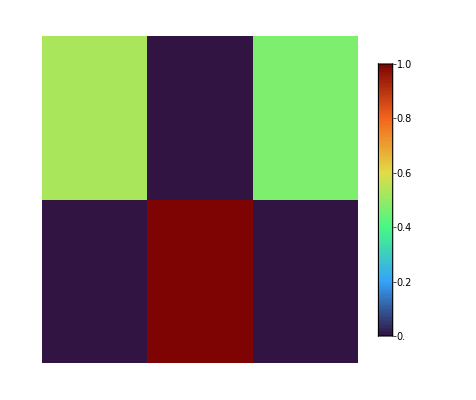

```mathematica
PosProbDisTimePlot[P2]
```

#### Valor de expectación respecto al tiempo

```mathematica
Clear@ExpValVsTimePlot
```

```mathematica
ExpValVsTimePlot[expecValue_List,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->All,
PlotStyle->Thickness[0.005],
GridLines->{Range[Automatic,Automatic,50],Range[Automatic,Automatic,20]},
GridLinesStyle->Thin,
Evaluate@opts
]
```

```mathematica
ExpValVsTimePlot[{expecValues__List},opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,t],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->All,
Evaluate@opts
]
```

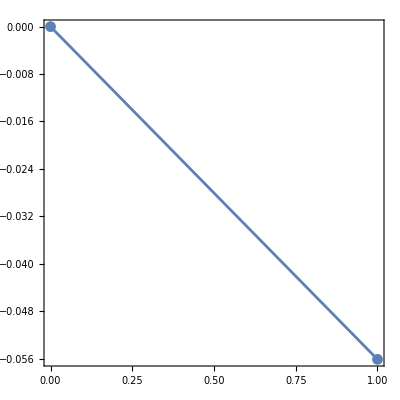

```mathematica
ExpValVsTimePlot[EV]
```

#### Valor de expectación para un tiempo fijo

```mathematica
FixedTimeExpValPlot[initCoinState_String,θ_,t_,results_List,nα_Integer,nϕ_Integer]:=Module[{data,alphaTicks,phiTicks,alphaVals,phiVals,alphaLines,phiLines},
(*Extraer datos {α,φ,valor}*)
data=Flatten[Function[{a,sublist},{a,#[[1]],#[[5,t+1]]}&/@sublist]@@@results,1];

(*Extraer valores únicos y ordenarlos*)
alphaVals=Sort@DeleteDuplicates[data[[All,1]]];
phiVals=Sort@DeleteDuplicates[data[[All,2]]];

(*Calcular líneas intermedias entre valores:fronteras de celdas*)
alphaLines=MovingAverage[alphaVals,2]//Flatten;
phiLines=MovingAverage[phiVals,2]//Flatten;

(*Ticks en múltiplos de π/10 y π/5*)
alphaTicks=Table[{2*i π/10,ToString[TraditionalForm[2*i π/nα]]},{i,0,nα}];
phiTicks=Table[{2*i*2π/nϕ,ToString[TraditionalForm[2*i*2π/nϕ]]},{i,0,nϕ}];

ListDensityPlot[data,
FrameLabel->{"α","ϕ"},
FrameTicks->{{phiTicks,None},{alphaTicks,None}},
ColorFunction->(ColorData["Rainbow"][Rescale[#,{-10,10}]]&),
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{"Rainbow",{-10,10}}],
InterpolationOrder->0,
ImageSize->200,
Epilog->{Table[{Black,Thin,Line[{{x,Min[phiVals]},{x,Max[phiVals]}}]},{x,alphaLines}],(*Líneas verticales*)
Table[{Black,Thin,Line[{{Min[alphaVals],y},{Max[alphaVals],y}}]},{y,phiLines}](*Líneas horizontales*)
}//Flatten,
PlotLabel->Row[{"c_0 = ",initCoinState,"     θ = ",θ,",     = ",t}]]]
```

#### Marcar el punto en la esfera de Bloch

```mathematica
PolarPoint[{r_,polar_,azimutal_}]:=Point[r*{Sin[polar] Cos[azimutal],Sin[polar] Sin[azimutal],Cos[polar]}]
```

```mathematica
ClearAll@SphereGraph
```

```mathematica
SphereGraph[initCoinState_String,θ_,results_List]:=Module[{points,sphere},
points=Join@@(Function[{a,sublist},{a,#[[1]],#[[2]]}&/@sublist]@@@results);
sphere=Graphics3D[{
Opacity[0.95],Glow[SphereColor],Black,Sphere[],
Opacity[1],PointSize[0.02],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,1.2}}],

Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{-1.2,0,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,-1.2,0}}],
Thick,Gray,Arrowheads[Medium],Arrow[{{0,0,0},{0,0,-1.2}}],

Text[Style["",14,Black],{1.3,0,0}],
Text[Style["",14,Black],{0,1.3,0}],
Text[Style["",14,Black],{0,0,1.3}],

Green,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[points,#[[3]]=="Ganadora"&]}],
Red,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[points,#[[3]]=="Perdedora"&]}],
Black,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[points,#[[3]]=="Indeterminado"&]}],
Gray,Table[PolarPoint[{1,p[[1]],p[[2]]}],{p,Select[points,#[[3]]=="No se puede determinar"&]}]
},
Boxed->False,
PlotLabel->Row[{"c_0 = ",initCoinState,",    θ = ",θ}]
]
]
```

## Pruebas

```mathematica
state0
```

{1.,0.}

```mathematica
coin0=state0;
θ=π;
α=π/2;
ϕ=π;
t=100;
R=CalculateData[coin0,θ,α,ϕ,t];
```

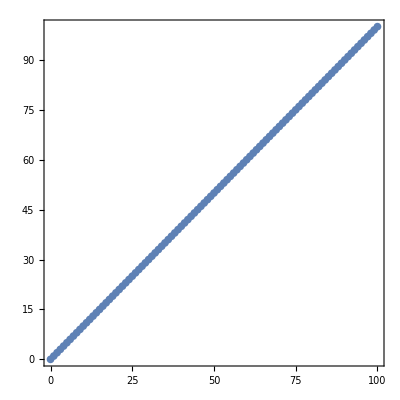

```mathematica
ExpValVsTimePlot[R[[2]]]
```

### Paradoja

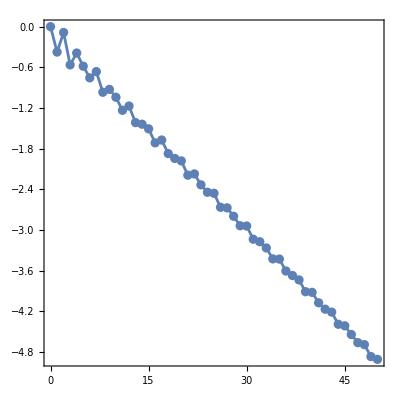

```mathematica
coin0=plusX;
θ=π;
α=0.39π;
ϕ=1.3π;
t=50;
R1=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R1[[2]]]
```

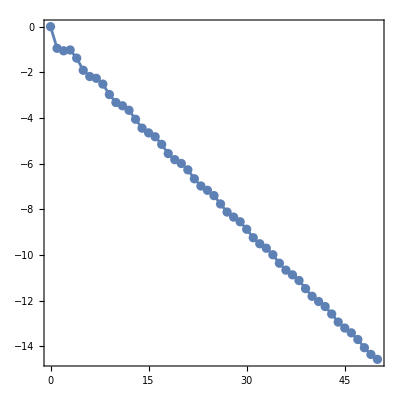

```mathematica
coin0=plusX;
θ=3π/2;
α=0.39π;
ϕ=1.3π;
t=50;
R2=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R2[[2]]]
```

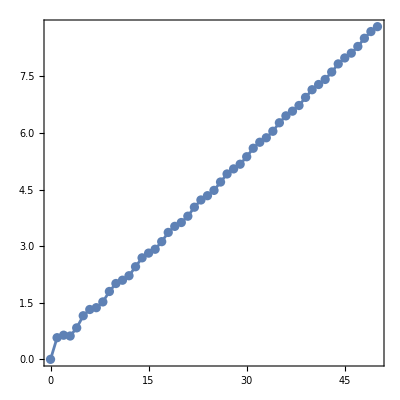

```mathematica
coin0=plusX;
θ=π+3π/2;
α=0.39π;
ϕ=1.3π;
t=50;
R3=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R3[[2]]]
```

```mathematica
coin0=plusX;

θ1=π;
α1=0.39π;
ϕ1=1.3π;

θ2=3π/2;
α2=0.39π;
ϕ2=1.3π;

t=50;

R3=CalculateData[coin0,{{θ1,α1,ϕ1},{θ2,α2,ϕ2}},t];

ExpValVsTimePlot[R3[[2]]]
```

-Graphics-

### Paradoja 2

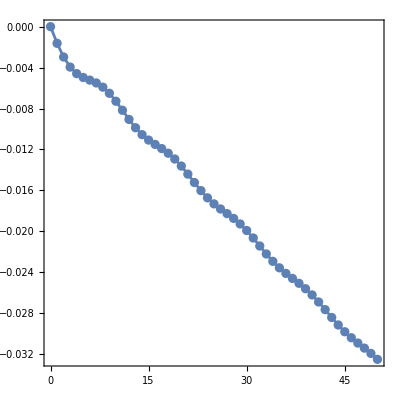

```mathematica
coin0=plusX;
θ=π/8+0.1π;
α=0.33π;
ϕ=0.06π;
t=50;
R3=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R3[[2]]]
```

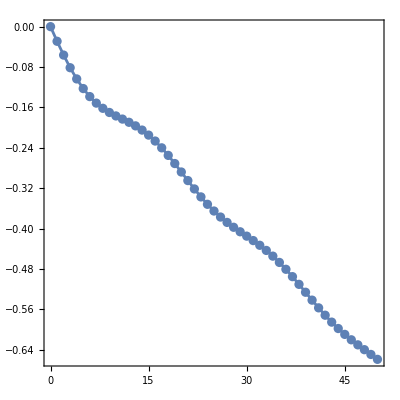

```mathematica
coin0=plusX;
θ=π/8;
α=0.33π;
ϕ=0.06π;
t=50;
R3=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R3[[2]]]
```

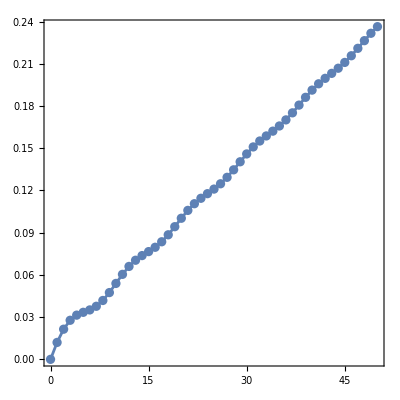

```mathematica
coin0=plusX;
θ=2(π/8);
α=0.33π;
ϕ=0.06π;
t=50;
R4=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R4[[2]]]
```

```mathematica
θ=.;
α=.;
ϕ=.;
expCoin[θ,α,ϕ]//FullSimplify//MatrixForm
```

(Cos[θ/2]-ⅈ Cos[α] Sin[θ/2] | Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]-Sin[ϕ])
Sin[α] Sin[θ/2] (-ⅈ Cos[ϕ]+Sin[ϕ]) | Cos[θ/2]+ⅈ Cos[α] Sin[θ/2])